# πK→πK and ππ→KK̄ scattering parameterizations as of last update in review: J.R.Pelaez and A.Rodas , Phys.Rept. 969 (2022) 1-126, 2010.11222 [hep-ph] ( previous papers on: arXiv:1602.08404, arXiv:1807.04543, arXiv:2001.08153 Correspondence: arodas@wm.edu (Version 05/2021)

```mathematica
SetOptions[EvaluationNotebook[],WindowSize->{800,900}]
```

## General Parameters

definition of masses and some other constants

```mathematica
physval={mp-> 0.13957,mk-> 0.496, me-> 0.547,mep->0.957,CONV->0.389379};
```

```mathematica
M=0.13957;
```

```mathematica
Mp=0.13957;
```

```mathematica
Mk=0.496;
```

```mathematica
Me=0.547;
```

```mathematica
Mep=0.957;
```

```mathematica
((Mk^2+Mp^2)+2 √((Mk^2-Mp^2)^2+Mk^2 Mp^2))/5
```

0.14785

## General Definitions

definition of the conformal variable w, momenta and phase space.

definition of the Chebyshev Polynomials used for g00 ππ---> KK

definition of the error function. Computed in quadrature from the parameter errors.

```mathematica
su=Mk^2-Mp^2;
sadler=0.236431(*GeV*);
y[s_]:=((s-su)/(s+su))^2;
w[s_,s0_,α_]=(√y[s]-α √(y[s0]-y[s]))/(√y[s]+α √(y[s0]-y[s]));
```

```mathematica
kp[s_]=√(s/4-mp^2);
```

```mathematica
kk[s_]=√(s/4-mk^2);
kk2[s_]=√(s/4-mk^2)HeavisideTheta[s-4 Mk^2];
```

```mathematica
ke[s_]=√(s/4-me^2);
```

```mathematica
σp[s_]=√(1-(4 mp^2)/s);
σk[s_]=√(1-(4 mk^2)/s);
```

```mathematica
kel[s_]:=1/2 √((s-(mp+mk)^2)(s-(mp-mk)^2)/s);
```

```mathematica
kinel[s_]:=1/2 √((s-(me+mk)^2)(s-(me-mk)^2)/s);
kinel2[s_]:=1/2 √((s-(mep+mk)^2)(s-(mep-mk)^2)/s);
```

```mathematica
σel[s_]=2 kel[s]/(√s);
σinel[s_]=2 kinel[s]/(√s);
x1[t_]:=2 (√t-2 Mk)/(1.47(*GeV*)-2 Mk)-1;
x2[t_]:=2 (√t-1.47(*GeV*))/(2(*GeV*)-1.47(*GeV*))-1;
```

```mathematica
Δerr[f_,r_,Δr_,n_]:=√(∑_(i=1)^n (D[f, r[[i,1]]])^2 Δr[[i,2]]^2);
Needs["NumericalCalculus`"]
Δerr2[f_,r_,Δr_,n_]:=√(∑_(i=1)^n (ND[f,r[[i,1]],r[[i,2]],WorkingPrecision->8,Terms->6])^2 Δr[[i,2]]^2);
h=0.000000001;
Δerr3[f_,r_,Δr_,n_]:=√(∑_(i=1)^n ((f/.r[[i,1]]->r[[i,2]]+Δr[[i,2]])-(f/.r))^2);
Δerr4[f_,r_,Δr_,n_]:=√(∑_(i=1)^n (((f-(f/.r[[i,1]]->r[[i,2]]-h))/h)/.r)^2 Δr[[i,2]]^2);
```

## UFD and CFD parametrizations for the l < 4 partial waves

PWA for L<4 defined below 2 GeV^2. The effect of higher L>3 partial waves is negligible up to that maximum energy.

### S32 - Wave

```mathematica
S32parUFD={s320-> 1.84^2,s32α-> 1.4,s32b0-> 2.1468,s32b1-> 3.9558,s32b2->3.1547};
S32parCFD={s320-> 1.84^2,s32α-> 1.4,s32b0-> 2.2083,s32b1-> 3.4598,s32b2->3.1333};
```

```mathematica
ΔS32par={Δs320->0,Δs32α->0,Δs32b0-> 0.027,Δs32b1-> 0.13,Δs32b2-> 0.32};
```

```mathematica
cotδs32conf[s_]=s^(1/2)/(2 kel[s])1/(Mp^2+Mk^2-s)(s32b0+s32b1 w[s,s320,s32α]+s32b2 w[s,s320,s32α]^2);
```

```mathematica
Clear[ts32]
ts32[s_]:=1/(cotδs32conf[s]-ⅈ);
```

```mathematica
δs32conf[s_]=ArcCot[cotδs32conf[s]];
```

```mathematica
δs32[s_]=δs32conf[s];
```

```mathematica
Δδs32[s_]:=Δerr[δs32[s],S32parCFD,ΔS32par,Length[S32parCFD]];
```

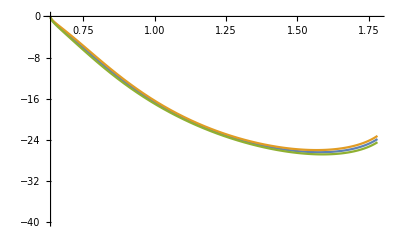

```mathematica
δs32Plot=Plot[{δs32[e^2]180/π/.S32parCFD/.physval,(δs32[e^2]+Δδs32[e^2])180/π/.S32parCFD/.physval,(δs32[e^2]-Δδs32[e^2])*180/π/.S32parCFD/.physval},{e,Mp+Mk,1.78},PlotRange-> {-40,0}]
```

```mathematica
Abs[w[1.74^2,s320,s32α]/.S32par]
```

ReplaceAll::reps: {S32par} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Abs[(0.86077-√(-0.740925+(-0.226536+s320)^2/(0.226536+s320)^2) s32α)/(0.86077+√(-0.740925+(-0.226536+s320)^2/(0.226536+s320)^2) s32α)/.S32par]

### S12 - Wave

```mathematica
S12parUFD={s120-> 1.1^2,s12α-> 1.15,s12b0-> 0.4021,s12b1-> 0.2222,s12a->-5.4568,s12b->8.112,s12c->-1.6539,s12phi0->-0.08225,s12phi1->4.6424,s12sr->1.4009^2 ,s12e1->1,s12G1->0.44275,s12sr2->1.8133^2,s12e2->0.1787,s12G2->0.32415};


S12parCFD={s120-> 1.1^2,s12α-> 1.15,s12b0-> 0.40326,s12b1-> 0.17259,s12a->-5.5285,s12b->8.244,s12c->-1.6174,s12phi0->-0.00179,s12phi1->4.6475,s12sr->1.4116^2 ,s12e1->1,s12G1->0.4394,s12sr2->1.8001^2,s12e2->0.1384,s12G2->0.2526};

S12parelCFD={s120-> 1.1^2,s12α-> 1.15,s12b0-> 0.403,s12b1-> 0.173};
S12parelUFD={s120-> 1.1^2,s12α-> 1.15,s12b0-> 0.402,s12b1-> 0.222};
```

```mathematica
ΔS12par={Δs120->0,Δs12α->0,Δs12b0-> 0.0064,Δs12b1-> 0.031,Δs12a->0.03,Δs12b->0.08,Δs12c->0.04,Δs12phi0->0.031,Δs12phi1->0.16,Δs12sr->0.011,Δs12e1->0,Δs12G1->0.024,Δs12sr2->0.062,Δs12e2->0.026,Δs12G2->0.10};

ΔS12parel={Δs120->0,Δs12α->0,Δs12b0-> 0.0064,Δs12b1-> 0.031};
```

```mathematica
cotδs12conf[s_]=s^(1/2)/(2 kel[s])1/(s-sadler)(s12b0+s12b1 w[s,s120,s12α]);
```

```mathematica
ts12conf[s_]=s^(1/2)/(2 kel[s])1/(cotδs12conf[s]-ⅈ);
```

```mathematica
δs12conf[s_]=ArcCot[cotδs12conf[s]];
```

```mathematica
δ00m=δ00conf[sm00]+π;
```

```mathematica
δ00mp=D[δ00conf[s], s]/.s-> sm00;
```

```mathematica
δs12[s_]=δs12conf[s];
```

```mathematica
Δδs12[s_]:=Δerr[δs12[s],S12parCFD,ΔS12par,Length[S12parCFD]];
```

```mathematica
pole[pars_]:=√(NSolve[(cotδs12conf[s]+ⅈ==0)/.physval/.pars,s][[1,1]][[2]])
```

```mathematica
Δpole[pars_,errpars_,n_]:=(resultr=0;resulti=0;parsh=Table[pars,{j,1,n}];
Do[parsh[[i]][[i,2]]=pars[[i,2]]-errpars[[i,2]];
resultr=resultr+(Re[pole[pars]-pole[parsh[[i]]]])^2;
resulti=resulti+(Im[pole[pars]-pole[parsh[[i]]]])^2;
,{i,1,n}];
Return[√resultr+ⅈ √resulti]);
```

```mathematica
pole[S12parelCFD]
pole[S12parelUFD]
```

0.673231+0.330889 ⅈ

0.651417+0.335692 ⅈ

```mathematica
Δpole[S12parelCFD,ΔS12parel,Length[S12parelCFD]]
Δpole[S12parelUFD,ΔS12parel,Length[S12parelUFD]]
```

0.0128539+0.00504465 ⅈ

0.0140324+0.00535565 ⅈ

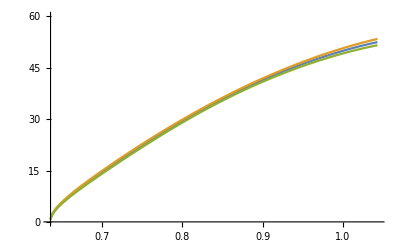

```mathematica
δs12Plot=Plot[{δs12[e^2]180/π/.S12parCFD/.physval,(δs12[e^2]+Δδs12[e^2])180/π/.S12parCFD/.physval,(δs12[e^2]-Δδs12[e^2])*180/π/.S12parCFD/.physval},{e,Mp+Mk,Me+Mk},PlotRange-> {0,60}]
```

```mathematica
sh=(mk+me)^2;
kelh=√((sh-(mp+mk)^2) (sh-(mk-mp)^2)/sh)/2;

ps121[s_]=1+s12a kel[s]^2+s12b kel[s]^4;
ps122[s_]=1+s12c kel[s]^2;

Ps121[s_]=(s12sr-s) /cotδs12conf[sh]+s12e1 s12G1 ps121[s]/ps121[s12sr] (kel[s]-kelh)/(kel[s12sr]-kelh);

Ps122[s_]=s12e2 s12G2 ps122[s]/ps122[s12sr2](kel[s]-kelh)/(kel[s12sr2]-kelh);

Qs122[s_]=(1-s12e2) s12G2 ps122[s]/ps122[s12sr2](kinel[s]/kinel[s12sr2])HeavisideTheta[s-(Me+Mk)^2];


S121[s_]=(s12sr-s+I(Ps121[s]))/(s12sr-s-I (Ps121[s]));

S122[s_]=(s12sr2-s+I(Ps122[s]-Qs122[s]))/(s12sr2-s-I (Ps122[s]+Qs122[s]));

S12b[s_]=Exp[2I kinel[s] (s12phi0+kinel[s]^2 s12phi1)HeavisideTheta[s-(Me+Mk)^2]];


S12[s_]=S121[s] S122[s] S12b[s];

Clear[ts12]
ts12[s_]:=Piecewise[{{1/(cotδs12conf[s]-ⅈ),s<(Me+Mk)^2},{(S12[s]-1)/(2 I),s>(Me+Mk)^2}}];(*If[s<(Me+Mk)^2,1/(cotδs12conf[s]-ⅈ),(S12[s]-1)/(2 I)]*)
Δargs12[s_]:=Δerr4[Arg[ts12[s]],S12parCFD,ΔS12par,Length[S12parCFD]]
Δmods12[s_]:=Δerr4[Abs[ts12[s]],S12parCFD,ΔS12par,Length[S12parCFD]]
```

```mathematica
Arg[ts12[1.4]]/.S12parCFD/.physval
Δargs12[1.4]/.S12parCFD/.physval//Timing
Δmods12[1.4]/.S12parCFD/.physval//Timing
```

1.16652

{0.095916,0.0259343}

{0.076667,0.0144469}

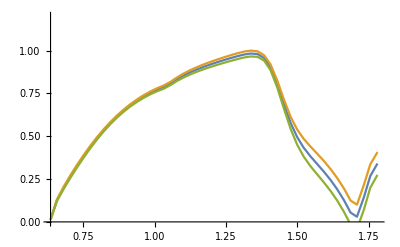

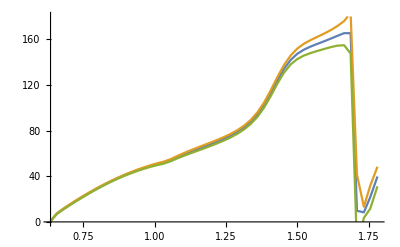

```mathematica
modts12plot=Plot[{Abs[ts12[e^2]]/.S12parCFD/.physval,(Abs[ts12[e^2]]+Δmods12[e^2])/.S12parCFD/.physval,(Abs[ts12[e^2]]-Δmods12[e^2])/.S12parCFD/.physval},{e,Mp+Mk,1.78},PlotRange-> {0,1.2},MaxRecursion->0,PlotPoints->50]

phasets12plot=Plot[{Arg[ts12[e^2]]180/π/.S12parCFD/.physval,(Arg[ts12[e^2]]+Δargs12[e^2])180/π/.S12parCFD/.physval,(Arg[ts12[e^2]]-Δargs12[e^2])180/π/.S12parCFD/.physval},{e,Mp+Mk,1.78},PlotRange-> {0,180},MaxRecursion->0,PlotPoints->50]
```

```mathematica
Abs[w[1.02^2,s120,s12α]/.S12parCFD]
```

0.404754

### P32 - Wave

```mathematica
P32parUFD={p320-> 1.84^2,p32α-> 1.45,p32b0->-9.188,p32b1->-3.1516,p32b2-> 0.56942};

P32parCFD={p320-> 1.84^2,p32α-> 1.45,p32b0->-8.3877,p32b1->-2.3756,p32b2->0.880549};
```

```mathematica
ΔP32par={Δp320->0,Δp32α->0,Δp32b0->2.4,Δp32b1-> 6.6,Δp32b2-> 0.17};
```

```mathematica
cotδp32conf[s_]=s^(1/2)/(2 kel[s]^3)(p32b0+p32b1 w[s,p320,p32α])s/(s-p32b2);
cotδp32confsr[s_]=s^(1/2)/2(p32b0+p32b1 w[s,p320,p32α])s/(s-p32b2);
```

```mathematica
tp32[s_]=1/(cotδp32conf[s]-ⅈ);
```

```mathematica
δp32conf[s_]=ArcCot[cotδp32conf[s]];
```

```mathematica
δp32[s_]:=δp32conf[s];
```

```mathematica
Δδp32[s_]:=Δerr[δp32[s],P32parCFD,ΔP32par,Length[P32parCFD]];
```

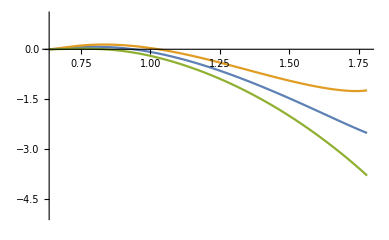

```mathematica
δp32Plot=Plot[{δp32[e^2]180/π/.P32parCFD/.physval,(δp32[e^2]+Δδp32[e^2])180/π/.P32parCFD/.physval,(δp32[e^2]-Δδp32[e^2])*180/π/.P32parCFD/.physval},{e,Mp+Mk,1.78},PlotRange-> {-5,1}]
```

```mathematica
a132=1/SeriesCoefficient[Series[cotδp32confsr[s],{s,(mk+mp)^2,1}],{s,(mk+mp)^2,0}]/.P32parCFD/.physval
b132=-a132^2 SeriesCoefficient[Series[cotδp32confsr[s],{s,(mk+mp)^2,1}],{s,(mk+mp)^2,1}](2 √((Mp+Mk)^2/(4 Mk Mp)))^2 /.P32parCFD/.physval
```

0.538261

-19.7611

```mathematica
a132 Mp^3
Δerr3[1/SeriesCoefficient[Series[cotδp32confsr[s],{s,(mk+mp)^2,1}],{s,(mk+mp)^2,0}] Mp^3,P32parCFD,ΔP32par,Length[P32parCFD]]/.P32parCFD/.physval
b132 Mp^5
Δerr3[-(1/SeriesCoefficient[Series[cotδp32confsr[s],{s,(mk+mp)^2,1}],{s,(mk+mp)^2,0}])^2 SeriesCoefficient[Series[cotδp32confsr[s],{s,(mk+mp)^2,1}],{s,(mk+mp)^2,1}](2 √((Mp+Mk)^2/(4 Mk Mp)))^2 Mp^5,P32parCFD,ΔP32par,Length[P32parCFD]]/.P32parCFD/.physval
```

0.00146342

0.00108365

-0.00104658

0.000832584

### P12 - Wave

```mathematica
P12parUFD={p120-> 1.1^2,Mkstar->0.89552,p12α-> 1.15,p12b0-> 0.9703,p12b1->0.5629,p12b2-> 2.6558,p12a1->-2.065,p12a2->-2.1146,p12a3->-1.335,p12sr1->0.8961^2,p12G1->0.03371,p12sr2->1.344^2,p12e2->0.04893,p12G2->0.2178,p12sr3->1.6465^2,p12e3->0.306,p12G3->0.306};

P12parCFD={p120-> 1.1^2,Mkstar-> 0.8946,p12α-> 1.15,p12b0-> 1.0544,p12b1->0.3603,p12b2->0.8884,p12a1->-1.600,p12a2->-1.7917,p12a3->-1.3687,p12sr1->0.8961^2,p12G1->0.04898,p12sr2->1.3474^2,p12e2->0.06746,p12G2->0.2120,p12sr3->1.6574^2,p12e3->0.3239,p12G3->0.2917};

P12parelUFD={p120-> 1.1^2,Mkstar->0.89552,p12α-> 1.15,p12b0-> 0.9703,p12b1->0.5629,p12b2-> 2.6558};

P12parelCFD={p120-> 1.1^2,Mkstar-> 0.8946,p12α-> 1.15,p12b0-> 1.0544,p12b1->0.3603,p12b2->0.8884};

P12parFOCUSCFD={p120-> 1.1^2,Mkstar-> 0.8947,p12α-> 1.15,p12b0-> 1.137,p12b1->0.45,p12b2-> 0.78,p12a1->-1.66,p12a2->-1.74,p12a3->-1.36,p12sr1->0.8961^2,p12G1->0.046,p12sr2->1.344^2,p12e2->0.067,p12G2->0.210,p12sr3->1.655^2,p12e3->0.320,p12G3->0.290};
```

```mathematica
ΔP12par={Δp120->0,ΔMkstar-> 0.0016,Δp12α-> 0,Δp12b0-> 0.025,Δp12b1->0.34,Δp12b2-> 0.83,Δp12a1->0.14,Δp12a2->0.27,Δp12a3->0.09,Δp12sr1->0,Δp12G1->0.005,Δp12sr2->0.032,Δp12e2->0.008,Δp12G2->0.043,Δp12sr3->0.016,Δp12e3->0.016,Δp12G3->0.018};

ΔP12parel={Δp120->0,ΔMkstar-> 0.0018,Δp12α-> 0,Δp12b0-> 0.025,Δp12b1->0.34,Δp12b2-> 0.83};

ΔP12parFOCUS={Δp120->0,ΔMkstar-> 0.0016,Δp12α-> 0,Δp12b0-> 0.048,Δp12b1->0.60,Δp12b2-> 1.01,Δp12a1->0.18,Δp12a2->0.28,Δp12a3->0.09,Δp12sr1->0,Δp12G1->0.005,Δp12sr2->0.032,Δp12e2->0.008,Δp12G2->0.042,Δp12sr3->0.016,Δp12e3->0.016,Δp12G3->0.018};

ΔP12parelFOCUS={Δp120->0,ΔMkstar-> 0.0018,Δp12α-> 0,Δp12b0-> 0.048,Δp12b1->0.60,Δp12b2-> 1.01};
```

{Δp120→0,ΔMkstar→0.0018,Δp12α→0,Δp12b0→0.024,Δp12b1→0.34,Δp12b2→0.83}

{Δp120→0,ΔMkstar→0.0018,Δp12α→0,Δp12b0→0.025,Δp12b1→0.34,Δp12b2→0.83}

```mathematica
cotδp12conf[s_]=s^(1/2)/(2 kel[s]^3)(Mkstar^2-s)(p12b0+p12b1 w[s,p120,p12α]+p12b2 w[s,p120,p12α]^2);
cotδp12confsr[s_]=s^(1/2)/2(Mkstar^2-s)(p12b0+p12b1 w[s,p120,p12α]+p12b2 w[s,p120,p12α]^2);
tp12el[s_]:=1/(cotδp12conf[s]-ⅈ);
```

```mathematica
δp12conf[s_]=ArcCot[cotδp12conf[s]];
```

```mathematica
Δδp12conf[s_]=Δerr[δp12conf[s],P12par,ΔP12par,Length[P12par]];
```

```mathematica
δp12m=δp12conf[sm11]+π;
ecotp12=NSolve[cotδp12conf[e^2]==0/.P12parCFD/.physval,e][[1]][[1,2]];
δp12[s_]=If[s<ecotp12^2,δp12conf[s],δp12conf[s]+π];
Δδp12[s_]:=Δerr[δp12[s],P12parCFD,ΔP12par,Length[P12parCFD]];
```

```mathematica
pole[pars_]:=(xm+ⅈ ym)/.FindMinimum[Abs[cotδp12conf[(xm+ⅈ ym)^2]+ⅈ]/.physval/.pars,{{xm,0.892},{ym,0.028}}][[2]]//Quiet
```

```mathematica
Δpole[pars_,errpars_,n_]:=(resultr=0;resulti=0;parsh=Table[pars,{j,1,n}];
Do[parsh[[i]][[i,2]]=pars[[i,2]]-errpars[[i,2]];
resultr=resultr+(Re[pole[pars]-pole[parsh[[i]]]])^2;
resulti=resulti+(Im[pole[pars]-pole[parsh[[i]]]])^2;
,{i,1,n}];
Return[√resultr+ⅈ √resulti]);
```

```mathematica
pole[P12parelUFD]
Δpole[P12parelUFD,ΔP12parel,Length[P12parelUFD]]
```

0.892516+0.0286554 ⅈ

0.00199776+0.00109295 ⅈ

```mathematica
pole[P12parelCFD]
Δpole[P12parelCFD,ΔP12parel,Length[P12parelCFD]]
```

0.891078+0.0269986 ⅈ

0.00192822+0.000912042 ⅈ

```mathematica
Plot3D[Abs[1/(cotδp12conf[(x+ⅈ y)^2]+ⅈ)/.physval/.P12parelUFD],{x,0.6,1},{y,0,0.1}]
```

-Graphics3D-

```mathematica
Δpole[P12parelUFD,ΔP12parel,Length[P12parelUFD]]
```

0.00199776+0.00109295 ⅈ

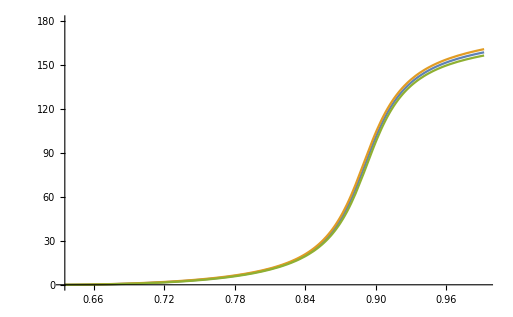

```mathematica
δp12Plot=Plot[{δp12[e^2]180/π/.P12parCFD/.physval,(δp12[e^2]+Δδp12[e^2])180/π/.P12parCFD/.physval,(δp12[e^2]-Δδp12[e^2])*180/π/.P12parCFD/.physval},{e,Mp+Mk,2 Mk},PlotRange-> {0,180}]
```

```mathematica
sh=(mk+me)^2;
kelh=√((sh-(mp+mk)^2) (sh-(mk-mp)^2)/sh)/2;

pp121[s_]=1+p12a1 kel[s]^2;
pp122[s_]=1+p12a2 kel[s]^2;
pp123[s_]=1+p12a3 kel[s]^2;
Pp121[s_]=(p12sr1-s)/cotδp12conf[sh]+p12G1 pp121[s]/pp121[p12sr1]*(kel[s]^2-kelh^2)/(kel[p12sr1]^2-kelh^2) kel[s]/kel[p12sr1];
Pp122[s_]=p12e2 p12G2 pp122[s]/pp122[p12sr2] (kel[s]^2-kelh^2)/(kel[p12sr2]^2-kelh^2) kel[s]/kel[p12sr2];
Pp123[s_]=p12e3 p12G3 pp123[s]/pp123[p12sr3] (kel[s]^2-kelh^2)/(kel[p12sr3]^2-kelh^2) kel[s]/kel[p12sr3];
Qp122[s_]=(1-p12e2) p12G2 pp122[s]/pp122[p12sr2](kinel[s]/kinel[p12sr2])^3 HeavisideTheta[s-(Me+Mk)^2];
Qp123[s_]=(1-p12e3) p12G3 pp123[s]/pp123[p12sr3](kinel[s]/kinel[p12sr3])^3 HeavisideTheta[s-(Me+Mk)^2];

Sp121[s_]=(p12sr1-s+I(Pp121[s]))/(p12sr1-s-I(Pp121[s]));

Sp122[s_]=(p12sr2-s+I(Pp122[s]-Qp122[s]))/(p12sr2-s-I(Pp122[s]+Qp122[s]));

Sp123[s_]=(p12sr3-s+I(Pp123[s]-Qp123[s]))/(p12sr3-s-I (Pp123[s]+Qp123[s]));

Sp12[s_]=Sp121[s] Sp122[s] Sp123[s];

tp12[s_]:=Piecewise[{{1/(cotδp12conf[s]-ⅈ),s<(Me+Mk)^2},{(Sp12[s]-1)/(2 I),s>(Me+Mk)^2}}];(*If[s<(Me+Mk)^2,1/(cotδp12conf[s]-ⅈ),(Sp12[s]-1)/(2 I)]*)
Δargp12[s_]:=Δerr4[Arg[tp12[s]],P12parCFD,ΔP12par,Length[P12parCFD]]
Δmodp12[s_]:=Δerr4[Abs[tp12[s]],P12parCFD,ΔP12par,Length[P12parCFD]]
```

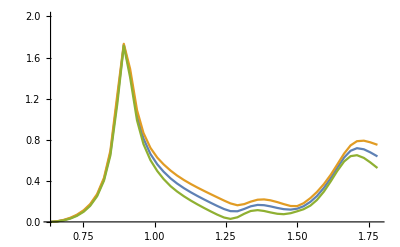

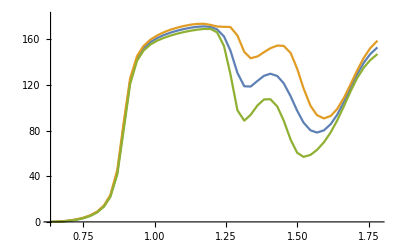

```mathematica
modtp12plot=Plot[{Abs[tp12[e^2]] √3/.P12parCFD/.physval,(Abs[tp12[e^2]]+Δmodp12[e^2])√3/.P12parCFD/.physval,(Abs[tp12[e^2]]-Δmodp12[e^2])√3/.P12parCFD/.physval},{e,Mp+Mk,1.78},PlotRange-> {0,2},MaxRecursion->0,PlotPoints->50]

phasetp12plot=Plot[{Arg[tp12[e^2]]180/π/.P12parCFD/.physval,(Arg[tp12[e^2]]+Δargp12[e^2])180/π/.P12parCFD/.physval,(Arg[tp12[e^2]]-Δargp12[e^2])180/π/.P12parCFD/.physval},{e,Mp+Mk,1.78},PlotRange-> {0,180},MaxRecursion->0,PlotPoints->50]
```

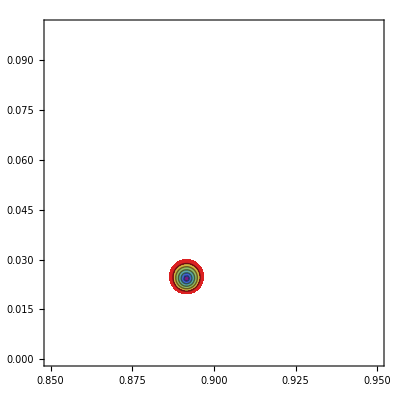

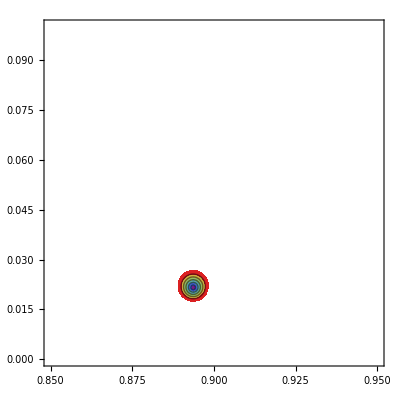

{1.52579×10^-7,{xp→0.891599,yp→0.0243207}}

{1.29564×10^-7,{xp→0.893636,yp→0.021615}}

```mathematica
ContourPlot[Abs[1+2 ⅈ σp[(x+ⅈ y)^2] (tp12el[(x+ⅈ y)^2])/.P12parCFD/.physval],{x,0.85,0.95},{y,0,0.1},PlotRange->{0.,0.1},Contours->5,ColorFunction->"Rainbow",PerformanceGoal->"Quality"]
ContourPlot[Abs[1+2 ⅈ σp[(x+ⅈ y)^2] (tp12el[(x+ⅈ y)^2])/.P12parFOCUSCFD/.physval],{x,0.85,0.95},{y,0,0.1},PlotRange->{0.,0.1},Contours->5,ColorFunction->"Rainbow",PerformanceGoal->"Quality"]
rho=FindMinimum[{Abs[1+2 ⅈ σp[(xp+ⅈ yp)^2] (tp12el[(xp+ⅈ yp)^2])/.P12parCFD/.physval]},{{xp,0.89},{yp,0.025}}]//Quiet
rho=FindMinimum[{Abs[1+2 ⅈ σp[(xp+ⅈ yp)^2] (tp12el[(xp+ⅈ yp)^2])/.P12parFOCUSCFD/.physval]},{{xp,0.89},{yp,0.025}}]//Quiet
```

```mathematica
a121=1/SeriesCoefficient[Series[cotδp12confsr[s],{s,(mk+mp)^2,1}],{s,(mk+mp)^2,0}]/.P12parCFD/.physval
b121=-a121^2 SeriesCoefficient[Series[cotδp12confsr[s],{s,(mk+mp)^2,1}],{s,(mk+mp)^2,1}](2 √((Mp+Mk)^2/(4 Mk Mp)))^2 /.P12parCFD/.physval
```

7.43842

89.1305

```mathematica
a121 Mp^3
Δerr3[1/SeriesCoefficient[Series[cotδp12confsr[s],{s,(mk+mp)^2,1}],{s,(mk+mp)^2,0}] Mp^3,P12parCFD,ΔP12par,Length[P12parCFD]]/.P12parCFD/.physval
b121 Mp^5
Δerr3[-(1/SeriesCoefficient[Series[cotδp12confsr[s],{s,(mk+mp)^2,1}],{s,(mk+mp)^2,0}])^2 SeriesCoefficient[Series[cotδp12confsr[s],{s,(mk+mp)^2,1}],{s,(mk+mp)^2,1}](2 √((Mp+Mk)^2/(4 Mk Mp)))^2 Mp^5,P12parCFD,ΔP12par,Length[P12parCFD]]/.P12parCFD/.physval
```

0.0202235

0.00413597

0.00472049

0.00174172

### D32 - Wave

```mathematica
D32parUFD={d320-> 1.84^2,d32α-> 1.45,d32b0-> -1.695,d32b1->-6.4979,d32b2->-36.091};

D32parCFD={d320-> 1.84^2,d32α-> 1.45,d32b0-> -1.777,d32b1->-7.8845,d32b2->-56.4066};
```

```mathematica
ΔD32par={Δd320->0,Δd32α->0,Δd32b0-> 0.12,Δd32b1-> 1.7,Δd32b2-> 8.7};
```

```mathematica
cotδd32conf[s_]=s^(1/2)/(2 kel[s]^5)(d32b0+d32b1 w[s,d320,d32α]+d32b2 w[s,d320,d32α]^2);
cotδd32confsr[s_]=s^(1/2)/2(d32b0+d32b1 w[s,d320,d32α]+d32b2 w[s,d320,d32α]^2);
```

```mathematica
td32[s_]:=1/(cotδd32conf[s]-ⅈ);
td32p[s_,q_]=1/(s^(1/2)/(2 q^5)(d32b0+d32b1 w[s,d320,d32α]+d32b2 w[s,d320,d32α]^2)-ⅈ);
```

```mathematica
δd32conf[s_]=ArcCot[cotδd32conf[s]];
```

```mathematica
δd32[s_]=δd32conf[s];
```

```mathematica
Δδd32[s_]:=Δerr[δd32[s],D32parCFD,ΔD32par,Length[D32parCFD]];
```

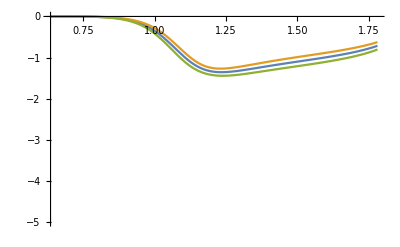

```mathematica
δd32Plot=Plot[{δd32[e^2]180/π/.D32parCFD/.physval,(δd32[e^2]+Δδd32[e^2])180/π/.D32parCFD/.physval,(δd32[e^2]-Δδd32[e^2])*180/π/.D32parCFD/.physval},{e,Mp+Mk,1.78},PlotRange-> {-5,0}]
```

```mathematica
Limit[Re[td32[x]/kel[x]^5]/.D32parCFD/.physval,x->(Mp+Mk)^2] Mp^5
```

-8.96568×10^-6

```mathematica
xpru=(Mp+Mk+0.0000000001)^2;
xpru2=(Mp+Mk+0.000001)^2;
td32[xpru]/kel[xpru]^5 Mp^5 /.D32parCFD/.physval
(Re[td32[xpru2]]/kel[xpru2]^5-Re[td32[xpru]]/kel[xpru]^5)/kel[xpru2]^2 Mp^7/.D32parCFD/.physval
```

-8.96568×10^-6+5.24738×10^-17 ⅈ

-1.15211×10^-8

```mathematica
a132=1/SeriesCoefficient[Series[cotδd32confsr[s],{s,(mk+mp)^2,1}],{s,(mk+mp)^2,0}]/.D32parCFD/.physval
b132=-a132^2 SeriesCoefficient[Series[cotδd32confsr[s],{s,(mk+mp)^2,1}],{s,(mk+mp)^2,1}](2 √((Mp+Mk)^2/(4 Mk Mp)))^2 /.D32parCFD/.physval
```

-0.169067

-3.36039

```mathematica
a132 Mp^5
Δerr3[1/SeriesCoefficient[Series[cotδd32confsr[s],{s,(mk+mp)^2,1}],{s,(mk+mp)^2,0}] Mp^5,D32parCFD,ΔD32par,Length[D32parCFD]]/.D32parCFD/.physval
b132 Mp^7
Δerr3[-(1/SeriesCoefficient[Series[cotδd32confsr[s],{s,(mk+mp)^2,1}],{s,(mk+mp)^2,0}])^2 SeriesCoefficient[Series[cotδd32confsr[s],{s,(mk+mp)^2,1}],{s,(mk+mp)^2,1}](2 √((Mp+Mk)^2/(4 Mk Mp)))^2 Mp^7,D32parCFD,ΔD32par,Length[D32parCFD]]/.D32parCFD/.physval
td32pru[s_]:=kel[s]^5(a132+b132 kel[s]^2);
```

-8.95405×10^-6

2.02497×10^-6

-3.46684×10^-6

8.64618×10^-7

```mathematica
xpru=0.71;
td32[xpru^2]/.D32parCFD/.physval
td32pru[xpru^2]/.physval
```

-0.0000114122+1.30238×10^-10 ⅈ

-0.0000112708

### D12 - Wave

```mathematica
D12parUFD={d12sr-> 1.4456^2,d12a->-0.52563,d12G->0.21966,d12e->0.46595,d12phi0->2.1677,d12phi1->-12.130};

D12parCFD={d12sr-> 1.4530^2,d12a->-0.82314,d12G->0.25583,d12e->0.45467,d12phi0->3.0497,d12phi1->-16.597};

ΔD12par={Δd12sr->0.006,Δd12a->0.16,Δd12G->0.009,Δd12e->0.006,Δd12phi0->0.26,Δd12phi1->1.7};
```

```mathematica
p1d12[s_]=1+d12a kel[s]^2;
Pd12[s_]=d12e d12G p1d12[s]/p1d12[d12sr] (kel[s]/kel[d12sr])^5;
Qd12[s_]=(1-d12e) d12G p1d12[s]/p1d12[d12sr] (kinel[s]/kinel[d12sr])^5 HeavisideTheta[s-(Me+Mk)^2];
Sd12[s_]=(d12sr-s+I (Pd12[s]-Qd12[s]))/(d12sr-s-I (Pd12[s]+Qd12[s]));
Sd12sr[s_]=(d12sr-s+I (Pd12[s]))/(d12sr-s-I (Pd12[s]));
Sbd12[s_]=Piecewise[{{Exp[2 I (kinel[s]^5 d12phi0+kinel2[s]^5 d12phi1)],s>(Mk+Mep)^2},{Exp[2 I (kinel[s]^5 d12phi0)HeavisideTheta[s-(Me+Mk)^2]],s<(Mk+Mep)^2}}];

td12[s_]:=(Sd12[s] Sbd12[s]-1)/(2 I);
td12sr[s_]=(Sd12sr[s]-1)/(2 I);
Δmodd12[s_]:=Δerr4[Abs[td12[s]],D12parCFD,ΔD12par,Length[D12parCFD]];
Δargd12[s_]:=Δerr4[Arg[td12[s]],D12parCFD,ΔD12par,Length[D12parCFD]];
```

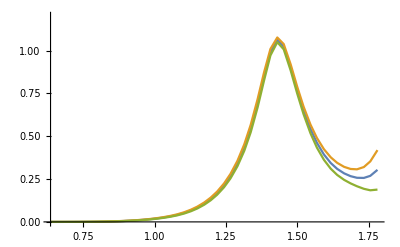

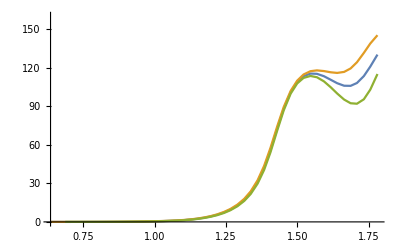

```mathematica
modtd12plot=Plot[{Abs[td12[e^2]] √5/.D12parCFD/.physval,(Abs[td12[e^2]]+Δmodd12[e^2])√5/.D12parCFD/.physval,(Abs[td12[e^2]]-Δmodd12[e^2])√5/.D12parCFD/.physval},{e,Mp+Mk,1.78},PlotRange-> {0,1.2},MaxRecursion->0,PlotPoints->50]

phasetd12plot=Plot[{Arg[td12[e^2]]180/π/.D12parCFD/.physval,(Arg[td12[e^2]]+Δargd12[e^2])180/π/.D12parCFD/.physval,(Arg[td12[e^2]]-Δargd12[e^2])180/π/.D12parCFD/.physval},{e,Mp+Mk+0.0001,1.78},PlotRange-> {0,160},MaxRecursion->0,PlotPoints->50]
```

```mathematica
Limit[Re[td12[x]/kel[x]^5]/.D12parCFD/.physval,x->(Mp+Mk)^2] Mp^5
```

0.0000528235

```mathematica
xpru=(Mp+Mk+0.0000001)^2;
xpru2=(Mp+Mk+0.00001)^2;
Re[td12[xpru]/kel[xpru]^5 Mp^5 ]/.D12parCFD/.physval
Δerr3[(td12[xpru])/kel[xpru]^5 Mp^5 ,D12parCFD,ΔD12par,Length[D12parCFD]]/.D12parCFD/.physval
(Re[td12[xpru2]]/kel[xpru2]^5-Re[td12[xpru]]/kel[xpru]^5)/kel[xpru2]^2 Mp^7/.D12parCFD/.physval
Δerr3[(td12[xpru2]/kel[xpru2]^5-td12[xpru]/kel[xpru]^5)/kel[xpru2]^2 Mp^7 ,D12parCFD,ΔD12par,Length[D12parCFD]]/.D12parCFD/.physval
```

0.0000528235

5.06128×10^-6+0. ⅈ

8.5185×10^-8

4.35753×10^-9+0. ⅈ

```mathematica
Series[td12sr[s],{s,(mk+mp)^2,4}]/.physval /.D12parCFD
a121=Re[SeriesCoefficient[Series[td12sr[s],{s,(mk+mp)^2,4}],{s,(mk+mp)^2,5/2}]] Mp^5(2 √((Mp+Mk)^2/(4 Mk Mp)))^5/.D12parCFD/.physval 
Δerr3[Re[SeriesCoefficient[Series[td12sr[s],{s,(mk+mp)^2,4}],{s,(mk+mp)^2,5/2}]] Mp^5(2 √((Mp+Mk)^2/(4 Mk Mp)))^5 ,D12parCFD,ΔD12par,Length[D12parCFD]]/.D12parCFD/.physval
b121=SeriesCoefficient[Series[td12sr[s],{s,(mk+mp)^2,5}],{s,(mk+mp)^2,7/2}] Mp^7(2 √((Mp+Mk)^2/(4 Mk Mp)))^7/.D12parCFD/.physval 
Δerr3[Re[SeriesCoefficient[Series[td12sr[s],{s,(mk+mp)^2,4}],{s,(mk+mp)^2,7/2}]] Mp^7(2 √((Mp+Mk)^2/(4 Mk Mp)))^7 ,D12parCFD,ΔD12par,Length[D12parCFD]]/.D12parCFD/.physval
t121pru[s_]:=.0120714 (s-0.4035679729)^(5/2)+0.03965512034385074 (s-0.4035679729)^(7/2);
```

0.0121347 (s-0.403568)^(5/2)+0.0398445 (s-0.403568)^(7/2)+O[s-0.403568]^(9/2)

0.0000528593

5.06517×10^-6

0.0000197287

1.75578×10^-6

### F12 - Wave

```mathematica
F12parUFD={f12sr-> 1.801^2,f12a->-0.88,f12G->0.47,f12e->0.181};

F12parCFD={f12sr->1.839^2,f12a->-1.060,f12G->0.6010,f12e->0.1726};

ΔF12par={Δf12sr->0.047,Δf12a->0.10,Δf12G->0.05,Δf12e->0.006};
```

```mathematica
p1f12[s_]=1+f12a kel[s]^2;
Pf12[s_]=f12e f12G p1f12[s]/p1f12[f12sr] (kel[s]/kel[f12sr])^7;
Qf12[s_]=(1-f12e) f12G p1f12[s]/p1f12[f12sr] (kinel[s]/kinel[f12sr])^7 HeavisideTheta[s-(Me+Mk)^2];
Sf12[s_]=(f12sr-s+I (Pf12[s]-Qf12[s]))/(f12sr-s-I (Pf12[s]+Qf12[s]));

tf12[s_]=(Sf12[s]-1)/(2 I);
Δmodf12[s_]:=Δerr4[Abs[tf12[s]],F12parCFD,ΔF12par,Length[F12parCFD]];
Δargf12[s_]:=Δerr4[Arg[tf12[s]],F12parCFD,ΔF12par,Length[F12parCFD]];
```

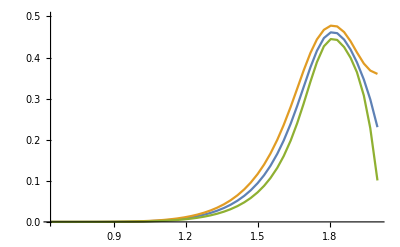

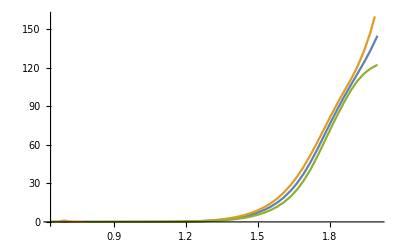

```mathematica
modtf12plot=Plot[{Abs[tf12[e^2]] √7/.F12parCFD/.physval,(Abs[tf12[e^2]]+Δmodf12[e^2])√7/.F12parCFD/.physval,(Abs[tf12[e^2]]-Δmodf12[e^2])√7/.F12parCFD/.physval},{e,Mp+Mk,2},PlotRange-> {0,0.5},MaxRecursion->0,PlotPoints->50]

phasetf12plot=Plot[{Arg[tf12[e^2]]180/π/.F12parCFD/.physval,(Arg[tf12[e^2]]+Δargf12[e^2])180/π/.F12parCFD/.physval,(Arg[tf12[e^2]]-Δargf12[e^2])180/π/.F12parCFD/.physval},{e,Mp+Mk,2},PlotRange-> {0,160},MaxRecursion->0,PlotPoints->50]
```

### g00 - Wave

```mathematica
g00parUFD={g0phi0-> 226.5,g0b1->23.633,g0b2-> 29.365, g0b3-> 0.62593,g0c0->0.46158,g0c1->-0.26740,g0c2-> 0.10916,g0c3->-0.0781,g0b12-> 35.345,g0b22->4.4361,g0b32->-32.912,g0b42->-15.950,g0b52->7.4074,g0c12->-0.04078,g0c22->-0.0103,g0c32->-0.0231,g0c42->0.02059,s000-> 4 mk^2,z00-> mp,B000-> 7.14,B001-> -25.3,B002-> -33.2,B003-> -26.2,sm00->0.850^2,d00-> 226.5 π/180,c00-> -81 π/180};

g00parCFD={g0phi0-> 226.5,g0b1->23.9892,g0b2-> 29.5197, g0b3->0.7136,g0c0->0.4464,g0c1-> -0.2356,g0c2-> 0.1012,g0c3-> -0.0873,g0b12-> 35.345,g0b22->4.0755,g0b32->-29.086,g0b42->-12.5945,g0b52->8.4680,g0c12->-0.04078,g0c22->-0.01573,g0c32->-0.02264,g0c42->0.0276,s000-> 4 mk^2,z00-> mp,B000-> 7.14,B001-> -25.3,B002-> -33.2,B003-> -26.2,sm00->0.850^2,d00-> 226.5 π/180,c00-> -81 π/180};
```

```mathematica
Δg00par={Δg0phi0->1.3,Δg0b1-> 1.3,Δg0b2-> 1.3, Δg0b3-> 1.6,Δg0c0->0.008,Δg0c1->0.013,Δg0c2-> 0.01,Δg0c3->0.009,Δg0b12->0,Δg0b22->2.6,Δg0b32-> 5.2,Δg0b42-> 2.2,Δg0b52->2.4,Δg0c12-> 0,Δg0c22->0.00848,Δg0c32-> 0.00715,Δg0c42-> 0.00646,Δs000-> 0,Δz00-> 0,ΔB000-> 0.227,ΔB001-> 0.521,ΔB002-> 1.178,ΔB003-> 2.262,Δsm00->0,dΔ00-> 1.3 π/180,Δc00-> 294.18 π/180};
```

```mathematica
S0par={s000-> 4 mk^2,z00-> mp,B000-> 7.136,B001-> -25.353,B002-> -33.194,B003-> -26.232,sm00->0.850^2,d00-> 226.492 π/180,c00-> -80.627 π/180,B00-> 93.334 π/180,C00-> 48.670 π/180,D00-> -88.306 π/180,ϵ001-> 4.928,ϵ002-> -15.098, ϵ003-> 4.671,ϵ004-> 0.320};
```

```mathematica
ΔS0par={Δs000-> 0,Δz00-> 0,ΔB000-> 0.227,ΔB001-> 0.521,ΔB002-> 1.178,ΔB003-> 2.262,Δsm00->0,dΔ00-> 1.298 π/180,Δc00-> 294.18 π/180,ΔB00-> 2.282 π/180,ΔC00-> 2.925 π/180,ΔD00-> 4.05 π/180,Δϵ001-> 0.227,Δϵ002-> 0.728, Δϵ003-> 0.056,Δϵ004-> 0.34};
```

```mathematica
tmin1=4 Mk^2;
tmax1=1.47^2;
tmin2=1.47^2;
tmax2=2^2;
x1[t_]=2(√t-√tmin1)/(√tmax1-√tmin1)-1;
x2[t_]=2(√t-√tmin2)/(√tmax2-√tmin2)-1;

g0ϕ1[t_]:=((g0phi0+g0b1-g0b2+g0b3)+g0b1 ChebyshevT[1,x1[t]]+g0b2 ChebyshevT[2,x1[t]]+g0b3 ChebyshevT[3,x1[t]]);
g0Mod1[t_]:=(g0c0+g0c1 ChebyshevT[1,x1[t]]+g0c2 ChebyshevT[2,x1[t]]+g0c3 ChebyshevT[3,x1[t]]);
g0ϕ2[t_]:=((g0ϕ1[tmax1]+g0b12-g0b22+g0b32-g0b42+g0b52)+g0b12 ChebyshevT[1,x2[t]]+g0b22 ChebyshevT[2,x2[t]]+g0b32 ChebyshevT[3,x2[t]]+g0b42 ChebyshevT[4,x2[t]]+g0b52 ChebyshevT[5,x2[t]]);
g0Mod2[t_]:=((g0Mod1[tmax1]+g0c12-g0c22+g0c32-g0c42) +g0c12*ChebyshevT[1,x2[t]]+g0c22 ChebyshevT[2,x2[t]]+g0c32 ChebyshevT[3,x2[t]]+g0c42 ChebyshevT[4,x2[t]]);
g0ϕ[t_]:=Piecewise[{{g0ϕ1[t],t<1.47^2},{g0ϕ2[t],t>1.47^2}}];
Δg0ϕ[t_]:=Δerr[g0ϕ[t],g00parCFD,Δg00par,Length[g00parCFD]];
g0Mod[t_]:=Piecewise[{{g0Mod1[t],t<1.47^2},{g0Mod2[t],t>1.47^2}}];
Δg0Mod[t_]:=Δerr[g0Mod[t],g00parCFD,Δg00par,Length[g00parCFD]];
g00[t_]:=g0Mod[t]Exp[I g0ϕ[t] π/180];

sM00=0.850^2;
cotδ00conf[s_]=s^(1/2)/(2 kp[s])mp^2/(s-1/2 z00^2)(z00^2/(mp s^(1/2))+B000+B001 w[s,s000]+B002 w[s,s000]^2+B003 w[s,s000]^3);
δ00conf[s_]=ArcCot[cotδ00conf[s]];
δ00m=δ00conf[sm00]+π;
δ00mp=D[δ00conf[s], s]/.s-> sm00;
δ00pol1[s_]=d00(1-k2[s]/k2[sm00])^2+δ00m k2[s]/k2[sm00](2-k2[s]/k2[sm00])+k2[s](k2[sm00]-k2[s])(8δ00mp+c00 (k2[sm00]-k2[s])/mk^3);
ecot00=NSolve[cotδ00conf[e^2]==0/.S0par/.physval,e][[1]][[1,2]];
δ00[s_]=If[s<ecot00^2,δ00conf[s]180/π,If[s<sM00,(δ00conf[s]+π)180/π,If[s<4 Mk^2,δ00pol1[s]180/π,g0ϕ[s]]]];
Δδ00[s_]:=Δerr[δ00[s],g00parCFD,Δg00par,Length[g00parCFD]];
```

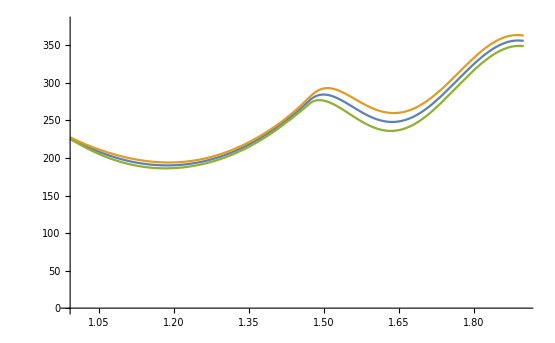

```mathematica
δ00Plot=Plot[{δ00[e^2]/.g00parCFD/.physval,(δ00[e^2]+Δδ00[e^2])/.g00parCFD/.physval,(δ00[e^2]-Δδ00[e^2])/.g00parCFD/.physval},{e,2Mp,1.9},PlotRange-> {0,380}]
```

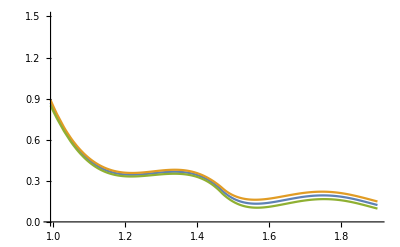

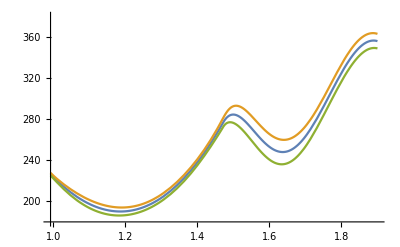

```mathematica
modg00plot=Plot[{g0Mod[e^2]/.g00parCFD/.physval,(g0Mod[e^2]+Δg0Mod[e^2])/.g00parCFD/.physval,(g0Mod[e^2]-Δg0Mod[e^2])/.g00parCFD/.physval},{e,2 Mk,1.9},PlotRange-> {0,1.5}]

phaseg00plot=Plot[{g0ϕ[e^2]/.g00parCFD/.physval,(g0ϕ[e^2]+Δg0ϕ[e^2])/.g00parCFD/.physval,(g0ϕ[e^2]-Δg0ϕ[e^2])/.g00parCFD/.physval},{e,2 Mk,1.9},PlotRange-> {180,380}]
```

### g11- Wave

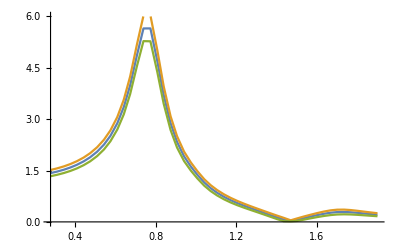

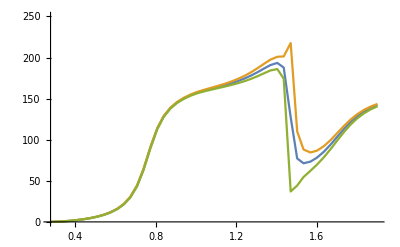

```mathematica
g11parUFD={g1c->1.28511,g1ra1-> 4.5411,g1b1->-0.16339, g1b2->0.3566,g1ga1->0.091,g1ga2->-0.0343,g1r1->0.7759,g1g1->0.15169,g1r2->1.4403,g1g2->0.3100,g1r3->1.72,g1g3->0.25};

g11parCFD={g1c->1.34573,g1ra1->3.8419,g1b1->-0.1665, g1b2->0.3535,g1ga1->0.081,g1ga2->0.055,g1r1->0.77563,g1g1->0.15089,g1r2->1.4636,g1g2->0.3385,g1r3->1.72,g1g3->0.25};

Δg11par={Δg1c->0.08,Δg1r1->0.64,Δg1b1->0.004, Δg1b2->0.015,Δg1ga1->0.024,Δg1ga2->0.03,Δg1r1->0.001,Δg1g1->0.0016,Δg1r2->0.031,Δg1g2->0.016,Δg1r3->0,Δg1g3->0};
g1gp[t_]:=√t(2 kp[t]/(√t))^3;
g1gk[t_]:=√t(2 kk2[t]/(√t))^3;
g1bw1[t_]:=g1r1^2/(g1r1^2-t-I g1g1 √t (2g1gp[t]+g1gk[t])/(2 g1r1(2 kp[g1r1^2]/g1r1)^3));
g1bw2[t_]:=g1r2^2/(g1r2^2-t-I g1g2 √t (2g1gp[t]+g1gk[t])/(2 g1r2(2 kp[g1r2^2]/g1r2)^3));
g1bw3[t_]:=g1r3^2/(g1r3^2-t-I g1g3 √t (2g1gp[t]+g1gk[t])/(2 g1r3(2 kp[g1r3^2]/g1r3)^3));
g11[t_]:=g1c/(√(1+g1ra1 kp[t]^2)√(1+g1ra1 kk2[t]^2)) (g1bw1[t]+(g1b1+g1b2 kk2[t]^2) g1bw2[t]+(g1ga1+g1ga2 kk2[t]^2)g1bw3[t]);
Arg2[f_]:=If[Arg[f]>0,Arg[f],Arg[f]+2 π];
Δmodg11[t_]:=Δerr4[Abs[g11[t]],g11parCFD,Δg11par,Length[g11parCFD]];
Δargg11[t_]:=Δerr4[Arg2[g11[t]],g11parCFD,Δg11par,Length[g11parCFD]];

modtg11plot=Plot[{Abs[g11[e^2]]/.g11parCFD/.physval,(Abs[g11[e^2]]+Δmodg11[e^2])/.g11parCFD/.physval,(Abs[g11[e^2]]-Δmodg11[e^2])/.g11parCFD/.physval},{e,2Mp,1.9},PlotRange-> {0,6},MaxRecursion->0,PlotPoints->50]

phasetg11plot=Plot[{Arg2[g11[e^2]]180/π/.g11parCFD/.physval,(Arg2[g11[e^2]]+Δargg11[e^2])180/π/.g11parCFD/.physval,(Arg2[g11[e^2]]-Δargg11[e^2])180/π/.g11parCFD/.physval},{e,2Mp,1.9},PlotRange-> {0,250},MaxRecursion->0,PlotPoints->50]
```

### g02 - Wave

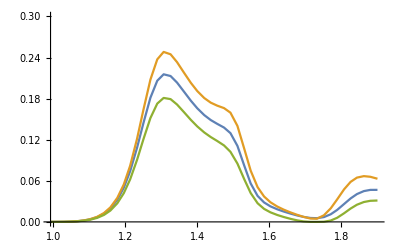

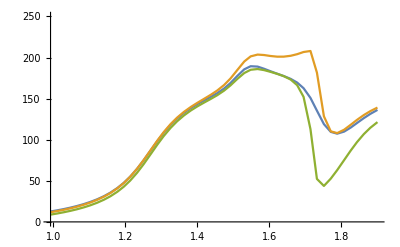

```mathematica
g02parUFD={g2c->1.8156,g2ra1->6.6790,g2b1->0.0703,g2ga1->0.0931,g2p1->-0.0492,g2p2->2.619,g2p3->-0.719,g2r1->1.2712,g2g1->0.1866,g2r2->1.5221,g2g2->0.1083,g2r3->1.8063,g2g3->0.2006};

g02parCFD={g2c->1.79752,g2ra1->6.84926,g2b1->0.0831,g2ga1->0.1039,g2p1->-0.0815,g2p2->2.579,g2p3->-0.877,g2r1->1.2720,g2g1->0.1841,g2r2->1.5215,g2g2->0.1156,g2r3->1.8003,g2g3->0.1803};

Δg02par={Δg2c->0.09,Δg2ra1->0.72,Δg2b1->0.016,Δg2ga1->0.02,Δg2p1->0.015,Δg2p2->0.16,Δg2p3->0.16,Δg2r1->0.0036,Δg2g1->0.009,Δg2r2->0.005,Δg2g2->0.0156,Δg2r3->0.0174,Δg2g3->0.0279};
g1gp[t_]:=√t(2 kp[t]/(√t))^3;
g1gk[t_]:=√t(2 kk2[t]/(√t))^3;
d2[x_]:=9+3 x^2+x^4;
g2bw1[t_]:=g2r1^2/(g2r1^2-t-I g2g1 g2r1 (kp[t]/kp[g2r1^2])^5 g2r1/(√t)d2[5 kp[g2r1^2]]/d2[5 kp[t]]);
g2bw2[t_]:=g2r2^2/(g2r2^2-t-I g2g2 g2r2 (kp[t]/kp[g2r2^2])^5 g2r2/(√t)d2[5 kp[g2r2^2]]/d2[5 kp[t]]);
g2bw3[t_]:=g2r3^2/(g2r3^2-t-I g2g3 g2r3 (kp[t]/kp[g2r3^2])^5 g2r3/(√t)d2[5 kp[g2r3^2]]/d2[5 kp[t]]);
g02g[t_]:=(g2c √((kp[t]kk[t])^5))/(√t √(1+g2ra1 kp[t]^4)√(1+g2ra1 kk2[t]^4)) ( Exp[I g2p1]g2bw1[t]+g2b1 Exp[I g2p2] g2bw2[t]+g2ga1  Exp[I g2p3]g2bw3[t]);
g02[t_]:=g2c/(2 √(1+g2ra1 kp[t]^4)√(1+g2ra1 kk2[t]^4)) ( Exp[I g2p1]g2bw1[t]+g2b1 Exp[I g2p2] g2bw2[t]+g2ga1  Exp[I g2p3]g2bw3[t]);
Arg2[f_]:=If[Arg[f]>0,Arg[f],Arg[f]+2 π];
Δmodg02g[t_]:=Δerr4[Abs[g02g[t]],g02parCFD,Δg02par,Length[g02parCFD]];
Δargg02[t_]:=Δerr4[Arg2[g02[t]],g02parCFD,Δg02par,Length[g02parCFD]];

modtg02plot=Plot[{Abs[g02g[e^2]]^2 5/.g02parUFD/.physval,(Abs[g02g[e^2]]+Δmodg02g[e^2])^2 5/.g02parCFD/.physval,(Abs[g02g[e^2]]-Δmodg02g[e^2])^2 5/.g02parCFD/.physval},{e,2Mk,1.9},PlotRange-> {0,0.3},MaxRecursion->0,PlotPoints->50]

phasetg02plot=Plot[{Arg2[g02[e^2]]180/π/.g02parUFD/.physval,(Arg2[g02[e^2]]+Δargg02[e^2])180/π/.g02parCFD/.physval,(Arg2[g02[e^2]]-Δargg02[e^2])180/π/.g02parCFD/.physval},{e,2Mk,1.9},PlotRange-> {0,250},MaxRecursion->0,PlotPoints->50]
```

### πK Isospin Amplitudes

```mathematica
zs[s_,t_]=1+2(s t)/((s-(Mp+Mk)^2)(s-(Mp-Mk)^2));
F12[s_,t_]=16π(ts12[s]+3LegendreP[1,zs[s,t]] tp12[s]+5LegendreP[2,zs[s,t]] td12[s]+7LegendreP[3,zs[s,t]] tf12[s])/σel[s];
F32[s_,t_]=16π(ts32[s]+3LegendreP[1,zs[s,t]] tp32[s]+5LegendreP[2,zs[s,t]] ts32[s])/σel[s];
imF12[s_,t_]=Im[F12[s,t]];
imF32[s_,t_]=Im[F32[s,t]];
```

### ππ--->KK Isospin Amplitudes

```mathematica
zt[t_,s_]=(2s+t-2(Mp^2+Mk^2))/(√(t-4 Mp^2)√(t-4 Mk^2));
G0[t_,s_]=16π √2(g00[t]+5LegendreP[2,zt[t,s]] g02[t](kp[t]kk[t])^2);
G1[t_,s_]=16π √2(3LegendreP[1,zt[t,s]] g11[t](kp[t] kk[t]));
imG0[s_,t_]=Im[G0[s,t]];
imG1[s_,t_]=Im[G1[s,t]];
```

## Regge Amplitudes πK

Regge approximation for the high-energy tail of the ππ scattering amplitude, now factorized for πK

### POMERON AMPLITUDE

#### Parameters Pomeron

```mathematica
reggepoparUFD={Subscript[β, P]->2.50,Subscript[β, P^p]->0.80,Subscript[α^p, P]-> 0.2,Subscript[c, P]-> 0.6,Subscript[c, P^p]->-0.38,b->2.4,sg->1,Subscript[α^p, P^p]->0.9,Subscript[α, P^p0]->0.52,fpk->0.67,rpk->0.05};
reggepoparCFD={Subscript[β, P]->2.50,Subscript[β, P^p]->0.80,Subscript[α^p, P]-> 0.2,Subscript[c, P]-> 0.6,Subscript[c, P^p]->-0.38,b->2.4,sg->1,Subscript[α^p, P^p]->0.9,Subscript[α, P^p0]->0.52,fpk->0.64,rpk->0.056};
Δreggepopar={Subscript[Δβ, P]->0.04,Subscript[Δβ, P^p]->0.05,Subscript[Δα^p, P]-> 0.1,Subscript[Δc, P]-> 1,Subscript[Δc, P^p]->0.4,Δb->0.2,Δsg->0,Subscript[Δα^p, P^p]->0,Subscript[Δα, P^p0]->0.02,Δfpk->0.02,Δrpk->0.001};
```

#### Formulas

```mathematica
P[s_,t_]:=Subscript[β, P] Subscript[ψ, P][t]Subscript[α, P][t](1+Subscript[α, P][t])/2 ⅇ^(b t)(s/sg)^(Subscript[α, P][t])
Pp[s_,t_]:=Subscript[β, P^p] Subscript[ψ, P^p][t](Subscript[α, P^p][t](1+Subscript[α, P^p][t]))/(Subscript[α, P^p][0](1+Subscript[α, P^p][0]))ⅇ^(b t)(s/sg)^(Subscript[α, P^p][t])
Subscript[α, P][t_]:=1+t Subscript[α^p, P]
Subscript[α, P^p][t_]:=Subscript[α, P^p0]+t Subscript[α^p, P^p]
Subscript[ψ, P][t_]:=ⅇ^(Subscript[c, P] t) 
Subscript[ψ, P^p][t_]:=ⅇ^(Subscript[c, P^p] t)
ν[s_,t_]:=s+t/2-2 M^2
ImF0t[s_,t_]:=fpk P[s,t]+rpk Pp[s,t]
ReF0t[s_,t_]:=fpk P[s,t] Log[(ν[s,0]+2 M^2)/(ν[s,0]-2 M^2)]/π+rpk Pp[s,t](Cos[π Subscript[α, P^p][0]]+1)/Sin[π Subscript[α, P^p][0]]
errImF0t[s_,t_]:=Δerr[ImF0t[s,t],reggepoparCFD,Δreggepopar,Length[reggepoparCFD]];
```

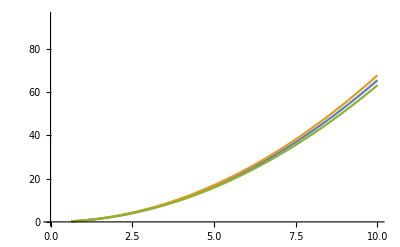

```mathematica
Plot[{ImF0t[e^2,0]/(√6)/.physval/.reggepoparCFD,(ImF0t[e^2,0]+errImF0t[e^2,0])/(√6)/.physval/.reggepoparCFD,(ImF0t[e^2,0]-errImF0t[e^2,0])/(√6)/.physval/.reggepoparCFD},{e,Mp+Mk,10},PlotRange-> {0,95}]
```

```mathematica
Pp[2^2,0]/(√6)/.physval
```

(2^(-1/2+2 α_(P^p0)) (1/sg)^(α_(P^p0)) β_(P^p))/(√3)

### ρ-Reggeon AMPLITUDE

#### Parameters

```mathematica
reggerhoparUFD={Subscript[β, ρ]->1.48,Subscript[α^p, ρ]->0.9,Subscript[α^pp, ρ]->-0.3,Subscript[α, ρ0]->0.53,Subscript[d, ρ]->2.4,Subscript[e, ρ]->0,Subscript[b, ρ]->2.4,sρ->1,gpk->0.7};
reggerhoparCFD={Subscript[β, ρ]->1.48,Subscript[α^p, ρ]->0.9,Subscript[α^pp, ρ]->-0.3,Subscript[α, ρ0]->0.53,Subscript[d, ρ]->2.4,Subscript[e, ρ]->0,Subscript[b, ρ]->2.4,sρ->1,gpk->0.52};
Δreggerhopar={Subscript[Δβ, ρ]->0.14,Subscript[Δα^p, ρ]->0,Subscript[Δα^pp, ρ]->0,Subscript[Δα, ρ0]->0.02,Subscript[Δd, ρ]->0.5,Subscript[Δe, ρ]->2.5,Subscript[Δb, ρ]->0.2,Δsρ->0,Δgpk->0.09};
```

#### Formulas

```mathematica
Subscript[α, ρ][t_]:=Subscript[α, ρ0]+t Subscript[α^p, ρ]+1/2 t^2 Subscript[α^pp, ρ]
Subscript[f, ρ]=Subscript[e, ρ]-Subscript[d, ρ]/2;
φ[t_]:=ⅇ^(Subscript[d, ρ] t+Subscript[f, ρ] t^2)
ImF1t[s_,t_]:=gpk Subscript[β, ρ](1+Subscript[α, ρ][t])/(1+Subscript[α, ρ][0])φ[t] ⅇ^(Subscript[b, ρ] t)(s/sρ)^(Subscript[α, ρ][t])
ReF1t[s_,t_]:=gpk (Cos[π Subscript[α, ρ][0]]-1)/Sin[π Subscript[α, ρ][0]] ImF1t[s,t]
errImF1t[s_,t_]:=Δerr[ImF1t[s,t],reggerhoparCFD,Δreggerhopar,Length[reggerhoparCFD]];
```

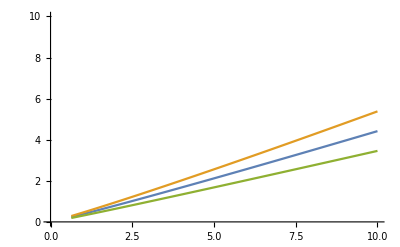

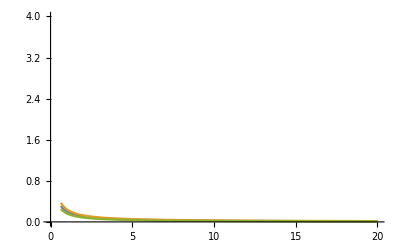

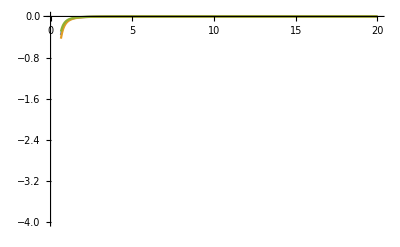

```mathematica
Plot[{ImF1t[e^2,0]/2/.physval/.reggerhoparCFD,(ImF1t[e^2,0]+errImF1t[e^2,0])/2/.physval/.reggerhoparCFD,(ImF1t[e^2,0]-errImF1t[e^2,0])/2/.physval/.reggerhoparCFD},{e,Mp+Mk,10},PlotRange-> {0,10}]
Plot[{(D[ImF1t[x,0],x]/.x->e^2)/2/.physval/.reggerhoparCFD,(D[(ImF1t[x,0]+errImF1t[x,0]),x]/.x->e^2)/2/.physval/.reggerhoparCFD,(D[(ImF1t[x,0]-errImF1t[x,0]),x]/.x->e^2)/2/.physval/.reggerhoparCFD},{e,Mp+Mk,20},PlotRange-> {0,4}]
Plot[{(D[ImF1t[x,0],{x,2}]/.x->e^2)/2/.physval/.reggerhoparCFD,(D[(ImF1t[x,0]+errImF1t[x,0]),{x,2}]/.x->e^2)/2/.physval/.reggerhoparCFD,(D[(ImF1t[x,0]-errImF1t[x,0]),{x,2}]/.x->e^2)/2/.physval/.reggerhoparCFD},{e,Mp+Mk,20},PlotRange-> {-4,0}]
```

```mathematica
D[ImF1t[x,0],x]/.x->e^2/.physval/.reggerhoparCFD
(D[(ImF1t[x,0]+errImF1t[x,0]),x]/.x->e^2)/2/.physval/.reggerhoparCFD
(D[(ImF1t[x,0]-errImF1t[x,0]),x]/.x->(Mk+Mp)^2)/2/.physval/.reggerhoparCFD
(D[ImF1t[x,0],{x,2}]/.x->e^2)/2/.physval
```

0.407888/((e^2)^0.47)

1/2 (0.407888/((e^2)^0.47)+(0.070596 (e^2)^0.06)/(√((e^2)^1.06)))

0.258227

(gpk (e^2/sρ)^(-2+α_ρ0) (-1+α_ρ0) α_ρ0 β_ρ)/(2 sρ^2)

### ρ VENEZIANO AMPLITUDE

#### Parameters

```mathematica
reggerparv={α0r->0.475,α0k->0.352,αpr->0.882,λ->13.4};
Δreggerparv={Δα0r->0,Δα0k->0,Δαpr->0,Δλ->4};
```

#### Formulas

```mathematica
αrho[t_]:=α0r+αpr t
αk[s_]:=α0k+αpr s
u[s_,t_]:=2(Mp^2+Mk^2)-s-t
Vkρ[s_,t_]:=(Gamma[1-αk[s]] Gamma[1-αrho[t]])/Gamma[1-αk[s]-αrho[t]]
ImF0tv[s_,t_]:=(λ (αpr s)^(α0r+αpr t))/(2π Gamma[α0r+αpr t])(*G0/√6*);
ImF1tv[s_,t_]:=(λ (αpr s)^(α0r+αpr t))/(2π Gamma[α0r+αpr t])(*G1/2*);
errImF1tv[s_,t_]:=Δerr[ImF1tv[s,t],reggerparv,Δreggerparv,Length[reggerparv]];
```

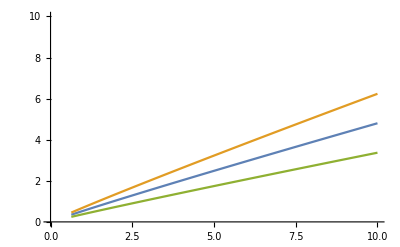

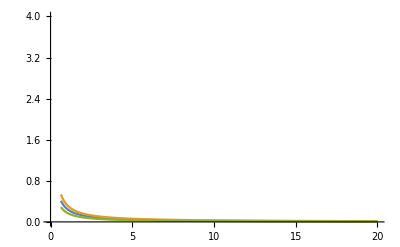

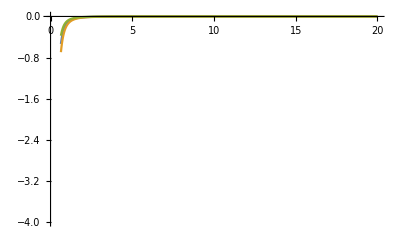

```mathematica
Plot[{ImF1tv[e^2,0]/2/.physval/.reggerparv,(ImF1tv[e^2,0]+errImF1tv[e^2,0])/2/.physval/.reggerparv,(ImF1tv[e^2,0]-errImF1tv[e^2,0])/2/.physval/.reggerparv},{e,Mp+Mk,10},PlotRange-> {0,10}]
Plot[{(D[ImF1tv[x,0],x]/.x->e^2)/2/.physval/.reggerparv,(D[(ImF1tv[x,0]+errImF1tv[x,0]),x]/.x->e^2)/2/.physval/.reggerparv,(D[(ImF1tv[x,0]-errImF1tv[x,0]),x]/.x->e^2)/2/.physval/.reggerparv},{e,Mp+Mk,20},PlotRange-> {0,4}]
Plot[{(D[ImF1tv[x,0],{x,2}]/.x->e^2)/2/.physval/.reggerparv,(D[(ImF1tv[x,0]+errImF1tv[x,0]),{x,2}]/.x->e^2)/2/.physval/.reggerparv,(D[(ImF1tv[x,0]-errImF1tv[x,0]),{x,2}]/.x->e^2)/2/.physval/.reggerparv},{e,Mp+Mk,20},PlotRange-> {-4,0}]
```

```mathematica
ImF1tv[e^2,0]/.physval/.reggerparv
```

1.07756 (e^2)^0.475

## Cross Sections πK

We define the total and differential πK cross sections.

Below 1.8^2 GeV^2is constructed from the PWA, above from  Regge amplitudes

### PWA Cross sections

Cross section constructed from the PWA amplitudes, defined below s=1.8^2 GeV^2

Definitions of Total cross section:

for the channels with I=1/2, 3/2

```mathematica
σ12[s_,t_]=CONV/(√((s-(mp+mk)^2)(s-(mp-mk)^2)))imF12[s,t];
```

```mathematica
σ32[s_,t_]=CONV/(√((s-(mp+mk)^2)(s-(mp-mk)^2)))imF32[s,t];
```

Definitions of differential cross section:

for the same conventions

```mathematica
σ12dt[s_,t_]=CONV/(16π (s-(mp+mk)^2)(s-(mp-mk)^2))Abs[F12[s,t]]^2;
```

```mathematica
σ32dt[s_,t_]=CONV/(16π (s-(mp+mk)^2)(s-(mp-mk)^2))Abs[F32[s,t]]^2;
```

### Regge Cross sections

Same conventions for the Regge amplitudes, defined above s=2 GeV^2

```mathematica
σ12R[s_,t_]=(4 π^2 CONV)/(√((s-(mp+mk)^2)(s-(mp-mk)^2)))(1/(√6)ImF0t[s,t]+ImF1t[s,t]);
```

```mathematica
σ32R[s_,t_]=(4 π^2 CONV)/(√((s-(mp+mk)^2)(s-(mp-mk)^2)))(1/(√6)ImF0t[s,t]-1/2 ImF1t[s,t]);
```

```mathematica
σ12dtR[s_,t_]=(16 π^4 CONV)/(16π (s-(mp+mk)^2)(s-(mp-mk)^2))(1/(√6)(ReF0t[s,t]^2+ImF0t[s,t]^2)+(ReF1t[s,t]^2+ImF1t[s,t]^2));
```

```mathematica
σ32dtR[s_,t_]=(16 π^4 CONV)/(16π(s-(mp+mk)^2)(s-(mp-mk)^2))(1/(√6)(ReF0t[s,t]^2+ImF0t[s,t]^2)-1/2(ReF1t[s,t]^2+ImF1t[s,t]^2));
```

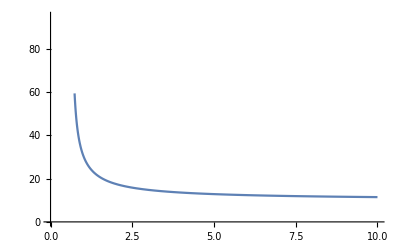

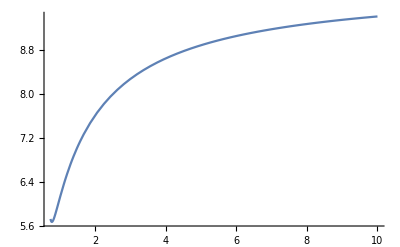

```mathematica
Plot[{σ12R[e^2,0]/.physval/.reggepoparCFD/.reggerhoparCFD},{e,Mp+Mk+0.1,10},PlotRange-> {0,95}]
Plot[{σ32R[e^2,0]/.physval/.reggepoparCFD/.reggerhoparCFD},{e,Mp+Mk+0.1,10},PlotRange-> All]
```

```mathematica
σ12R[1^2,0]/.physval
```

21.3011 (((fpk β_P)/sg+rpk (1/sg)^(α_(P^p0)) β_(P^p))/(√6)+gpk (1/sρ)^α_ρ0 β_ρ)

### Cross sections in the whole energy range

Cross sections for the whole energy region. PWA amplitudes below 2 GeV^2 and Regge amplitudes above

```mathematica
σ12T[s_,t_]=If[s<1.8^2,σ12[s,t],σ12R[s,t]];
```

```mathematica
σ32T[s_,t_]=If[s<1.8^2,σ32[s,t],σ32R[s,t]];
```

```mathematica
σ12dtT[s_,t_]=If[s<1.8^2,σ12dt[s,t],σ12dtR[s,t]];
```

```mathematica
σ32dtT[s_,t_]=If[s<1.8^2,σ32dt[s,t],σ32dtR[s,t]];
```

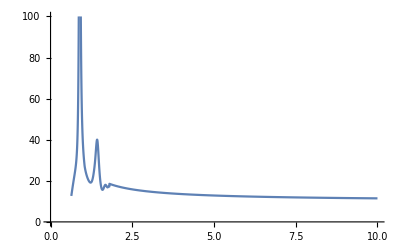

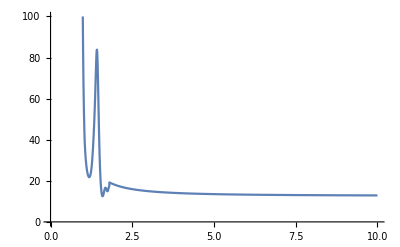

```mathematica
σ12PlotT=Plot[{σ12T[e^2,0]/.S12parCFD/.P12parCFD/.D12parCFD/.F12parCFD/.physval/.reggepoparCFD/.reggerhoparCFD},{e,Mp+Mk,10},PlotRange-> {0,100}]
σ12dtPlotT=Plot[{σ12dtT[e^2,0]/.S12parCFD/.P12parCFD/.D12parCFD/.F12parCFD/.physval/.reggepoparCFD/.reggerhoparCFD},{e,Mp+Mk,10},PlotRange-> {0,100}]
```

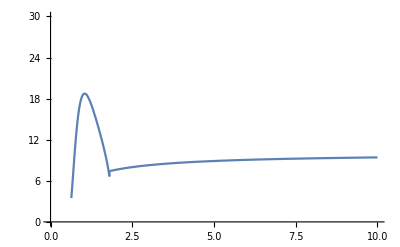

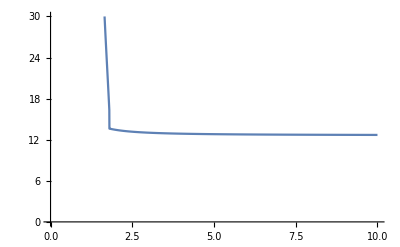

```mathematica
σ32PlotT=Plot[{σ32T[e^2,0]/.S32parCFD/.P32parCFD/.D32parCFD/.physval/.reggepoparCFD/.reggerhoparCFD},{e,Mp+Mk,10},PlotRange-> {0,30}]
σ32dtPlotT=Plot[{σ32dtT[e^2,0]/.S32parCFD/.P32parCFD/.D32parCFD/.physval/.reggepoparCFD/.reggerhoparCFD},{e,Mp+Mk,10},PlotRange-> {0,30}]
```

## Regge Amplitudes ππ--->KK

Veneziano approximation for the high-energy tail of the ππ--->KK scattering amplitude

### K1(892)-Reggeon amplitude

#### Parameters

```mathematica
reggeKparUFD={α0r->0.475,α0k->0.352,αpr->0.882,λ->11};
reggeKparCFD={α0r->0.475,α0k->0.352,αpr->0.882,λ->13.4};
ΔreggeKpar={Δα0r->0,Δα0k->0,Δαpr->0,Δλ->4};
```

#### Formulas

```mathematica
αrho[t_]:=α0r+αpr t
αk[s_]:=α0k+αpr s
u[s_,t_]:=2(Mp^2+Mk^2)-s-t
Vkρ[s_,t_]:=(Gamma[1-αk[s]] Gamma[1-αrho[t]])/Gamma[1-αk[s]-αrho[t]]
ImG0t[t_,s_]:=(√6 π λ (αpr t)^(α0k+αpr s))/Gamma[α0k+αpr s](*F0*)
ImG1t[t_,s_]:=(2π λ (αpr t)^(α0k+αpr s))/Gamma[α0k+αpr s](*2G1*)
ReG0t[t_,s_]:=(√6 π λ (αpr t)^(α0k+αpr s))/Gamma[α0k+αpr s] Cot[(α0k+αpr s)π](*F0*)
ReG1t[t_,s_]:=(2π λ (αpr t)^(α0k+αpr s))/Gamma[α0k+αpr s] Cot[(α0k+αpr s)π](*2G1*)
```

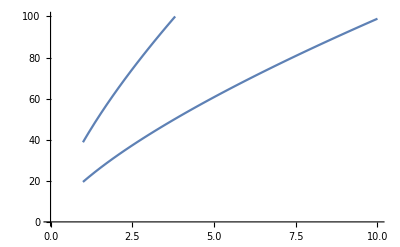

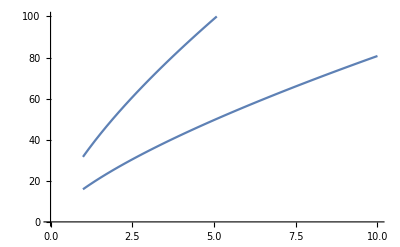

```mathematica
Show[Plot[{ReG0t[e^2,0]/.physval/.reggeKparCFD},{e,2 Mk,10},PlotRange-> {0,100}],Plot[{ImG0t[e^2,0]/.physval/.reggeKparCFD},{e,2 Mk,10},PlotRange-> {0,100}]]
Show[Plot[{ReG1t[e^2,0]/.physval/.reggeKparCFD},{e,2 Mk,10},PlotRange-> {0,100}],Plot[{ImG1t[e^2,0]/.physval/.reggeKparCFD},{e,2 Mk,10},PlotRange-> {0,100}]]
```

## Cross Sections ππ--->KK

We define the inelastic differential ππ--->KK cross sections.

Below 2^2 GeV^2is constructed from the PWA, above from  Regge amplitudes

### PWA Cross sections

Definitions of differential cross section:

for the same conventions

```mathematica
σ0dt[t_,s_]=CONV/(16π  t (t-4 Mp^2))Abs[G0[t,s]]^2;
```

```mathematica
σ1dt[t_,s_]=CONV/(16π  t (t-4 Mp^2))Abs[G1[t,s]]^2;
```

### Regge Cross sections

Same conventions for the Regge amplitudes, defined above s=2 GeV^2

```mathematica
σ0dtR[t_,s_]=CONV/(16π t (t-4 M^2))(ReG0t[t,s]^2+ImG0t[t,s]^2);
```

```mathematica
σ1dtR[t_,s_]=CONV/(16π t (t-4 M^2))(ReG1t[t,s]^2+ImG1t[t,s]^2);
```

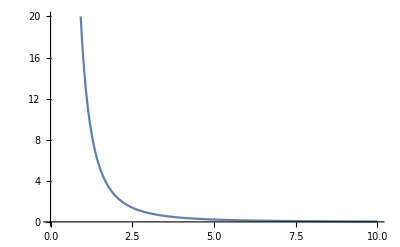

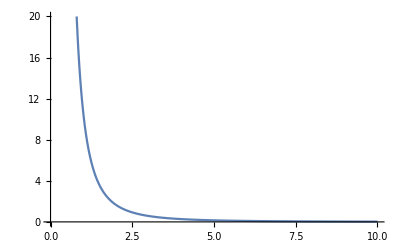

```mathematica
Plot[{σ0dtR[e^2,0]/.physval/.reggeKparCFD},{e,Mp+Mk+0.1,10},PlotRange-> {0,20}]
Plot[{σ1dtR[e^2,0]/.physval/.reggeKparCFD},{e,Mp+Mk+0.1,10},PlotRange->{0,20}]
```

### Cross sections in the whole energy range

Cross sections for the whole energy region. PWA amplitudes below 2 GeV^2 and Regge amplitudes above

```mathematica
σ0dtT[s_,t_]=If[s<2^2,σ0dt[s,t],σ0dtR[s,t]];
```

```mathematica
σ1dtT[s_,t_]=If[s<2^2,σ1dt[s,t],σ1dtR[s,t]];
```

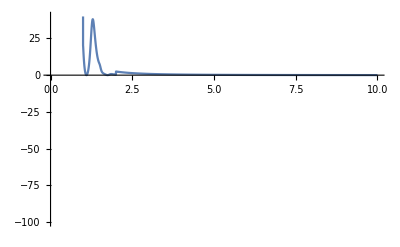

```mathematica
σ0dtPlotT=Plot[{σ0dtT[e^2,0]/.g00parCFD/.g02parCFD/.physval/.reggeKparCFD},{e,2Mk,10},PlotRange-> {-100,40}]
```

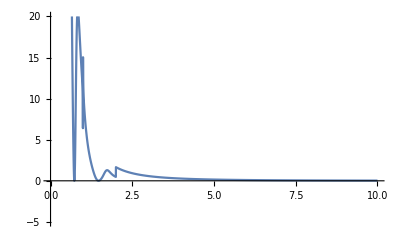

```mathematica
σ1dtPlotT=Plot[{σ1dtT[e^2,0]/.g11parCFD/.physval/.reggeKparCFD},{e,Mp+Mk,10},PlotRange-> {-5,20}]
```